```mathematica
(*** define the perturbation models and a few other functions are defined below*)

ClearAll["Global`*"]
glycolysisACE[ACE_,maxTime_, GLCo0_]:=(
variables = {
 AMP[t], ATP[t], BPG[t], F16P[t], F6P[t], G3P[t], G6P[t], GLCi[t], NADH[t], P2G[t], P3G[t], PEP[t], PYR[t], TRIO[t]
};

initialValues = {
 AMP[0] == 0.169126793522, ATP[0] == 2.88896546881, BPG[0] == 0.000272378466415, F16P[0] == 5.1230306063, F6P[0] == 1.35316959718, G3P[0] == 1.51464838664, G6P[0] == 5.2330035355, GLCi[0] == 0.0264527982732, NADH[0] == 0.570243405518, P2G[0] == 0.0219411145028, P3G[0] == 0.182294273857, PEP[0] == 0.0180777173497, PYR[0] == 2.26719823412, TRIO[0] == 2.6506857804
};

rates = { v GLT,v GLK,v GLYCO,v Treha,
v PGI, v PFK,v ALD,v G3PDH, v G3PA,
v GAPDH, v PGK, v PGM,  v ENO,v PYK,
v PDC, v SUC, v ADH,   v ATP,v AK};

rateEquations = {
v ADH -> -((VmADH*(ETOH*NAD - (ACE[t]*NADH[t])/KeqADH))/(KiADHNAD*KmADHETOH*(1 + (ETOH*KmADHNAD)/(KiADHNAD*KmADHETOH) + NAD/KiADHNAD + (ETOH*NAD)/(KiADHNAD*KmADHETOH) + (KmADHNADH*ACE[t])/(KiADHNADH*KmADHACE) + (ETOH*NAD*ACE[t])/(KiADHACE*KiADHNAD*KmADHETOH) + (KmADHNADH*NAD*ACE[t])/(KiADHNAD*KiADHNADH*KmADHACE) + NADH[t]/KiADHNADH + (ETOH*KmADHNAD*NADH[t])/(KiADHNAD*KiADHNADH*KmADHETOH) + (ACE[t]*NADH[t])/(KiADHNADH*KmADHACE) + (ETOH*ACE[t]*NADH[t])/(KiADHETOH*KiADHNADH*KmADHACE)))), v AK -> 133.333*(ADP^2 - (AMP[t]*ATP[t])/KeqAK), v ALD -> (VmALD*(F16P[t] - (KeqTPI*TRIO[t]^2)/(KeqALD*(1 + KeqTPI)^2)))/(KmALDF16P*(1 + F16P[t]/KmALDF16P + TRIO[t]/((1 + KeqTPI)*KmALDDHAP) + (KeqTPI*TRIO[t])/((1 + KeqTPI)*KmALDGAP) + (KeqTPI*F16P[t]*TRIO[t])/((1 + KeqTPI)*KmALDF16P*KmALDGAPi) + (KeqTPI*TRIO[t]^2)/((1 + KeqTPI)^2*KmALDDHAP*KmALDGAP))), v ATP -> (KATPASE*ATP[t]^nATP)/(KmATP^nATP + ATP[t]^nATP), v ENO -> (VmENO*(P2G[t] - PEP[t]/KeqENO))/(KmENOP2G*(1 + P2G[t]/KmENOP2G + PEP[t]/KmENOPEP)), v G3PA -> (VmG3PA*G3P[t])/(KmG3PAG3P*(1 + Phi/KmG3PAPhi)*(1 + G3P[t]/KmG3PAG3P)), v G3PDH -> (VmG3PDH*(-((NAD*G3P[t])/KeqG3PDH) + (NADH[t]*TRIO[t])/(1 + KeqTPI)))/(KmG3PDHDHAP*KmG3PDHNADH*(1 + ADP/KmG3PDHADP + ATP[t]/KmG3PDHATP + F16P[t]/KmG3PDHF16P)*(1 + NAD/KmG3PDHNAD + NADH[t]/KmG3PDHNADH)*(1 + G3P[t]/KmG3PDHG3P + TRIO[t]/((1 + KeqTPI)*KmG3PDHDHAP))), v GAPDH -> (-((VmGAPDHf*BPG[t]*NADH[t])/(KeqGAPDH*KmGAPDHGAP*KmGAPDHNAD)) + (KeqTPI*NAD*VmGAPDHf*TRIO[t])/((1 + KeqTPI)*KmGAPDHGAP*KmGAPDHNAD))/((1 + NAD/KmGAPDHNAD + NADH[t]/KmGAPDHNADH)*(1 + BPG[t]/KmGAPDHBPG + (KeqTPI*TRIO[t])/((1 + KeqTPI)*KmGAPDHGAP))), v GLK -> (VmGLK*(-((ADP*G6P[t])/KeqGLK) + ATP[t]*GLCi[t]))/(KmGLKATP*KmGLKGLCi*(1 + ADP/KmGLKADP + ATP[t]/KmGLKATP)*(1 + G6P[t]/KmGLKG6P + GLCi[t]/KmGLKGLCi)), v GLT -> (VmGLT*(GLCo - GLCi[t]/KeqGLT))/(KmGLTGLCo*(1 + GLCo/KmGLTGLCo + GLCi[t]/KmGLTGLCi + (alpha*GLCo*GLCi[t])/(KmGLTGLCi*KmGLTGLCo))), v GLYCO -> KGLYCOGEN*ATP[t]*G6P[t], v PDC -> (VmPDC*PYR[t]^nPDC)/(KmPDCPYR^nPDC*(1 + PYR[t]^nPDC/KmPDCPYR^nPDC)), v PFK -> (gR*VmPFK*ATP[t]*F6P[t]*(1 + ATP[t]/KmPFKATP + F6P[t]/KmPFKF6P + (gR*ATP[t]*F6P[t])/(KmPFKATP*KmPFKF6P)))/(KmPFKATP*KmPFKF6P*((L0*(1 + (CPFKAMP*AMP[t])/KPFKAMP)^2*(1 + (CiPFKATP*ATP[t])/KiPFKATP)^2*(1 + (CPFKATP*ATP[t])/KmPFKATP)^2*(1 + (CPFKF26BP*F26BP)/KPFKF26BP + (CPFKF16BP*F16P[t])/KPFKF16BP)^2)/((1 + AMP[t]/KPFKAMP)^2*(1 + ATP[t]/KiPFKATP)^2*(1 + F26BP/KPFKF26BP + F16P[t]/KPFKF16BP)^2) + (1 + ATP[t]/KmPFKATP + F6P[t]/KmPFKF6P + (gR*ATP[t]*F6P[t])/(KmPFKATP*KmPFKF6P))^2)), v PGI -> (VmPGI*(-(F6P[t]/KeqPGI) + G6P[t]))/(KmPGIG6P*(1 + F6P[t]/KmPGIF6P + G6P[t]/KmPGIG6P)), v PGK -> (VmPGK*(ADP*KeqPGK*BPG[t] - ATP[t]*P3G[t]))/(KmPGKATP*KmPGKP3G*(1 + ADP/KmPGKADP + ATP[t]/KmPGKATP)*(1 + BPG[t]/KmPGKBPG + P3G[t]/KmPGKP3G)), v PGM -> (VmPGM*(-(P2G[t]/KeqPGM) + P3G[t]))/(KmPGMP3G*(1 + P2G[t]/KmPGMP2G + P3G[t]/KmPGMP3G)), v PYK -> (VmPYK*(ADP*PEP[t] - (ATP[t]*PYR[t])/KeqPYK))/(KmPYKADP*KmPYKPEP*(1 + ADP/KmPYKADP + ATP[t]/KmPYKATP)*(1 + PEP[t]/KmPYKPEP + PYR[t]/KmPYKPYR)), v SUC -> KSUCC*ACE[t], v Treha -> KTREHALOSE*ATP[t]*G6P[t]
};

parameters = {
AXPsum -> 4.1, CPFKAMP -> 0.0845, CPFKATP -> 3.0, CPFKF16BP -> 0.397, CPFKF26BP -> 0.0174, CiPFKATP -> 100.0, ETOH -> 50.0, EXTERNAL -> 0.0, F26BP -> 0.02, GLCo -> GLCo0, KATPASE -> 68.8096317495,  KPFKAMP -> 0.0995, KPFKF16BP -> 0.111, KPFKF26BP -> 0.000682, KSUCC -> 19.6023811746(*GLYO flux*),  KeqADH -> 6.9*^-05, KeqAK -> 0.45, KeqALD -> 0.069, KeqENO -> 6.7, KeqG3PDH -> 4300.0, KeqGAPDH -> 0.0056263906277, KeqGLK -> 3800.0, KeqGLT -> 1.0, KeqPGI -> 0.314, KeqPGK -> 3200.0, KeqPGM -> 0.19, KeqPYK -> 6500.0, KeqTPI -> 0.045, KiADHACE -> 1.1, KiADHETOH -> 90.0, KiADHNAD -> 0.92, KiADHNADH -> 0.031, KiPFKATP -> 0.65, KmADHACE -> 1.11, KmADHETOH -> 17.0, KmADHNAD -> 0.17, KmADHNADH -> 0.11, KmALDDHAP -> 2.4, KmALDF16P -> 0.3, KmALDGAP -> 2.0, KmALDGAPi -> 10.0, KmATP -> 0.263159506089, KmENOP2G -> 0.04, KmENOPEP -> 0.5, KmG3PAG3P -> 4.21421727097, KmG3PAPhi -> 0.798017147071, KmG3PDHADP -> 1.60537927993, KmG3PDHATP -> 0.568725492711, KmG3PDHDHAP -> 0.4, KmG3PDHF16P -> 4.77110176421, KmG3PDHG3P -> 1.08899464691, KmG3PDHNAD -> 0.93, KmG3PDHNADH -> 0.023, KmGAPDHBPG -> 0.0098, KmGAPDHGAP -> 0.21, KmGAPDHNAD -> 0.09, KmGAPDHNADH -> 0.06, KmGLKADP -> 0.23, KmGLKATP -> 0.15, KmGLKG6P -> 30.0, KmGLKGLCi -> 0.08, KmGLTGLCi -> 1.1918, KmGLTGLCo -> 1.1918, KmPDCPYR -> 4.33, KmPFKATP -> 0.71, KmPFKF6P -> 0.1, KmPGIF6P -> 0.3, KmPGIG6P -> 1.4, KmPGKADP -> 0.2, KmPGKATP -> 0.3, KmPGKBPG -> 0.003, KmPGKP3G -> 0.53, KmPGMP2G -> 0.08, KmPGMP3G -> 1.2, KmPYKADP -> 0.53, KmPYKATP -> 1.5, KmPYKPEP -> 0.14, KmPYKPYR -> 21.0, L0 -> 0.66, NADSUM -> 1.0, Phi -> 1.20470265921,
 VmADH -> 834.684820559, VmALD -> 232.895576807, VmENO -> 462.025180445, VmG3PA -> 542.319235827, VmGAPDHf -> 419.560093466, VmGLK -> 329.958304618, VmGLT -> 136.494419254, VmPDC -> 223.978775021, VmPFK -> 183.616866462, VmPGI -> 467.754325004, VmPGK -> 1419.49486841, VmPGM -> 2762.32037661, VmPYK -> 1751.9596196, alpha -> 0.91, gR -> 5.12, nATP -> 1.0, nPDC -> 1.9, default compartment -> 1.0,
VmG3PDH -> 477.924460922,KGLYCOGEN -> 1.68983106019, KTREHALOSE -> 0.754128480342
};

assignments = {
NAD -> NADSUM - NADH[t], ADP -> AXPsum - AMP[t] - ATP[t]
};

(* Time evolution *)
odes = {
 AMP'[t] == 1.0*v AK , ATP'[t] == 1.0*v PGK +1.0*v PYK +1.0*v AK -1.0*v PFK -1.0*v ATP -4.0*v SUC -1.0*v GLYCO -1.0*v GLK -1.0*v Treha, BPG'[t] == 1.0*v GAPDH -1.0*v PGK, F16P'[t] == 1.0*v PFK -1.0*v ALD, F6P'[t] == 1.0*v PGI -1.0*v PFK, G3P'[t] == 1.0*v G3PDH -1.0*v G3PA, G6P'[t] == 1.0*v GLK -1.0*v PGI -1.0*v GLYCO -2.0*v Treha, GLCi'[t] == 1.0*v GLT -1.0*v GLK, NADH'[t] == 1.0*v GAPDH +3.0*v SUC -1.0*v G3PDH -1.0*v ADH, P2G'[t] == 1.0*v PGM -1.0*v ENO, P3G'[t] == 1.0*v PGK -1.0*v PGM, PEP'[t] == 1.0*v ENO -1.0*v PYK, PYR'[t] == 1.0*v PYK -1.0*v PDC, TRIO'[t] == 2.0*v ALD -1.0*v G3PDH -1.0*v GAPDH
};
timeCourse = NDSolve[Join[odes, initialValues]//.rateEquations//.assignments//.parameters, variables, {t, 0, maxTime}];
(* Plot the time evolution of the variables *)
amp[t_]:=AMP[t]/.parameters/.timeCourse;
atp[t_]:=ATP[t]/.parameters/.timeCourse;
bpg[t_]:=BPG[t]/.parameters/.timeCourse;
f16p[t_]:=F16P[t]/.parameters/.timeCourse;
f6p[t_]:=F6P[t]/.parameters/.timeCourse;
g3p[t_]:=G3P[t]/.parameters/.timeCourse;
g6p[t_]:=G6P[t]/.parameters/.timeCourse;
glci[t_]:=GLCi[t]/.parameters/.timeCourse;
nadh[t_]:=NADH[t]/.parameters/.timeCourse;
p2g[t_]:=P2G[t]/.parameters/.timeCourse;
p3g[t_]:=P3G[t]/.parameters/.timeCourse;
pep[t_]:=PEP[t]/.parameters/.timeCourse;
pyr[t_]:=PYR[t]/.parameters/.timeCourse;
trio[t_]:=TRIO[t]/.parameters/.timeCourse;
adp[t_]:=AXPsum - amp[t] - atp[t]/.parameters;
nad[t_]:=NADSUM - nadh[t]/.parameters;
{variables,parameters,timeCourse})

glycolysisACEremoveGLYCO[ACE_,maxTime_, GLCo0_]:=(
variables = {
 AMP[t], ATP[t], BPG[t], F16P[t], F6P[t], G3P[t], G6P[t], GLCi[t], NADH[t], P2G[t], P3G[t], PEP[t], PYR[t], TRIO[t]
};

initialValues = {
 AMP[0] == 0.169126793522, ATP[0] == 2.88896546881, BPG[0] == 0.000272378466415, F16P[0] == 5.1230306063, F6P[0] == 1.35316959718, G3P[0] == 1.51464838664, G6P[0] == 5.2330035355, GLCi[0] == 0.0264527982732, NADH[0] == 0.570243405518, P2G[0] == 0.0219411145028, P3G[0] == 0.182294273857, PEP[0] == 0.0180777173497, PYR[0] == 2.26719823412, TRIO[0] == 2.6506857804
};

rates = { v GLT,v GLK,v GLYCO,v Treha,
v PGI, v PFK,v ALD,v G3PDH, v G3PA,
v GAPDH, v PGK, v PGM,  v ENO,v PYK,
v PDC, v SUC, v ADH,   v ATP,v AK};

rateEquations = {
v ADH -> -((VmADH*(ETOH*NAD - (ACE[t]*NADH[t])/KeqADH))/(KiADHNAD*KmADHETOH*(1 + (ETOH*KmADHNAD)/(KiADHNAD*KmADHETOH) + NAD/KiADHNAD + (ETOH*NAD)/(KiADHNAD*KmADHETOH) + (KmADHNADH*ACE[t])/(KiADHNADH*KmADHACE) + (ETOH*NAD*ACE[t])/(KiADHACE*KiADHNAD*KmADHETOH) + (KmADHNADH*NAD*ACE[t])/(KiADHNAD*KiADHNADH*KmADHACE) + NADH[t]/KiADHNADH + (ETOH*KmADHNAD*NADH[t])/(KiADHNAD*KiADHNADH*KmADHETOH) + (ACE[t]*NADH[t])/(KiADHNADH*KmADHACE) + (ETOH*ACE[t]*NADH[t])/(KiADHETOH*KiADHNADH*KmADHACE)))), v AK -> 133.333*(ADP^2 - (AMP[t]*ATP[t])/KeqAK), v ALD -> (VmALD*(F16P[t] - (KeqTPI*TRIO[t]^2)/(KeqALD*(1 + KeqTPI)^2)))/(KmALDF16P*(1 + F16P[t]/KmALDF16P + TRIO[t]/((1 + KeqTPI)*KmALDDHAP) + (KeqTPI*TRIO[t])/((1 + KeqTPI)*KmALDGAP) + (KeqTPI*F16P[t]*TRIO[t])/((1 + KeqTPI)*KmALDF16P*KmALDGAPi) + (KeqTPI*TRIO[t]^2)/((1 + KeqTPI)^2*KmALDDHAP*KmALDGAP))), v ATP -> (KATPASE*ATP[t]^nATP)/(KmATP^nATP + ATP[t]^nATP), v ENO -> (VmENO*(P2G[t] - PEP[t]/KeqENO))/(KmENOP2G*(1 + P2G[t]/KmENOP2G + PEP[t]/KmENOPEP)), v G3PA -> (VmG3PA*G3P[t])/(KmG3PAG3P*(1 + Phi/KmG3PAPhi)*(1 + G3P[t]/KmG3PAG3P)), v G3PDH -> (VmG3PDH*(-((NAD*G3P[t])/KeqG3PDH) + (NADH[t]*TRIO[t])/(1 + KeqTPI)))/(KmG3PDHDHAP*KmG3PDHNADH*(1 + ADP/KmG3PDHADP + ATP[t]/KmG3PDHATP + F16P[t]/KmG3PDHF16P)*(1 + NAD/KmG3PDHNAD + NADH[t]/KmG3PDHNADH)*(1 + G3P[t]/KmG3PDHG3P + TRIO[t]/((1 + KeqTPI)*KmG3PDHDHAP))), v GAPDH -> (-((VmGAPDHf*BPG[t]*NADH[t])/(KeqGAPDH*KmGAPDHGAP*KmGAPDHNAD)) + (KeqTPI*NAD*VmGAPDHf*TRIO[t])/((1 + KeqTPI)*KmGAPDHGAP*KmGAPDHNAD))/((1 + NAD/KmGAPDHNAD + NADH[t]/KmGAPDHNADH)*(1 + BPG[t]/KmGAPDHBPG + (KeqTPI*TRIO[t])/((1 + KeqTPI)*KmGAPDHGAP))), v GLK -> (VmGLK*(-((ADP*G6P[t])/KeqGLK) + ATP[t]*GLCi[t]))/(KmGLKATP*KmGLKGLCi*(1 + ADP/KmGLKADP + ATP[t]/KmGLKATP)*(1 + G6P[t]/KmGLKG6P + GLCi[t]/KmGLKGLCi)), v GLT -> (VmGLT*(GLCo - GLCi[t]/KeqGLT))/(KmGLTGLCo*(1 + GLCo/KmGLTGLCo + GLCi[t]/KmGLTGLCi + (alpha*GLCo*GLCi[t])/(KmGLTGLCi*KmGLTGLCo))), v GLYCO -> KGLYCOGEN*ATP[t]*G6P[t], v PDC -> (VmPDC*PYR[t]^nPDC)/(KmPDCPYR^nPDC*(1 + PYR[t]^nPDC/KmPDCPYR^nPDC)), v PFK -> (gR*VmPFK*ATP[t]*F6P[t]*(1 + ATP[t]/KmPFKATP + F6P[t]/KmPFKF6P + (gR*ATP[t]*F6P[t])/(KmPFKATP*KmPFKF6P)))/(KmPFKATP*KmPFKF6P*((L0*(1 + (CPFKAMP*AMP[t])/KPFKAMP)^2*(1 + (CiPFKATP*ATP[t])/KiPFKATP)^2*(1 + (CPFKATP*ATP[t])/KmPFKATP)^2*(1 + (CPFKF26BP*F26BP)/KPFKF26BP + (CPFKF16BP*F16P[t])/KPFKF16BP)^2)/((1 + AMP[t]/KPFKAMP)^2*(1 + ATP[t]/KiPFKATP)^2*(1 + F26BP/KPFKF26BP + F16P[t]/KPFKF16BP)^2) + (1 + ATP[t]/KmPFKATP + F6P[t]/KmPFKF6P + (gR*ATP[t]*F6P[t])/(KmPFKATP*KmPFKF6P))^2)), v PGI -> (VmPGI*(-(F6P[t]/KeqPGI) + G6P[t]))/(KmPGIG6P*(1 + F6P[t]/KmPGIF6P + G6P[t]/KmPGIG6P)), v PGK -> (VmPGK*(ADP*KeqPGK*BPG[t] - ATP[t]*P3G[t]))/(KmPGKATP*KmPGKP3G*(1 + ADP/KmPGKADP + ATP[t]/KmPGKATP)*(1 + BPG[t]/KmPGKBPG + P3G[t]/KmPGKP3G)), v PGM -> (VmPGM*(-(P2G[t]/KeqPGM) + P3G[t]))/(KmPGMP3G*(1 + P2G[t]/KmPGMP2G + P3G[t]/KmPGMP3G)), v PYK -> (VmPYK*(ADP*PEP[t] - (ATP[t]*PYR[t])/KeqPYK))/(KmPYKADP*KmPYKPEP*(1 + ADP/KmPYKADP + ATP[t]/KmPYKATP)*(1 + PEP[t]/KmPYKPEP + PYR[t]/KmPYKPYR)), v SUC -> KSUCC*ACE[t], v Treha -> KTREHALOSE*ATP[t]*G6P[t]
};

parameters = {
AXPsum -> 4.1, CPFKAMP -> 0.0845, CPFKATP -> 3.0, CPFKF16BP -> 0.397, CPFKF26BP -> 0.0174, CiPFKATP -> 100.0, ETOH -> 50.0, EXTERNAL -> 0.0, F26BP -> 0.02, GLCo -> GLCo0, KATPASE -> 68.8096317495,  KPFKAMP -> 0.0995, KPFKF16BP -> 0.111, KPFKF26BP -> 0.000682, KSUCC -> 0(*GLYO flux*),  KeqADH -> 6.9*^-05, KeqAK -> 0.45, KeqALD -> 0.069, KeqENO -> 6.7, KeqG3PDH -> 4300.0, KeqGAPDH -> 0.0056263906277, KeqGLK -> 3800.0, KeqGLT -> 1.0, KeqPGI -> 0.314, KeqPGK -> 3200.0, KeqPGM -> 0.19, KeqPYK -> 6500.0, KeqTPI -> 0.045, KiADHACE -> 1.1, KiADHETOH -> 90.0, KiADHNAD -> 0.92, KiADHNADH -> 0.031, KiPFKATP -> 0.65, KmADHACE -> 1.11, KmADHETOH -> 17.0, KmADHNAD -> 0.17, KmADHNADH -> 0.11, KmALDDHAP -> 2.4, KmALDF16P -> 0.3, KmALDGAP -> 2.0, KmALDGAPi -> 10.0, KmATP -> 0.263159506089, KmENOP2G -> 0.04, KmENOPEP -> 0.5, KmG3PAG3P -> 4.21421727097, KmG3PAPhi -> 0.798017147071, KmG3PDHADP -> 1.60537927993, KmG3PDHATP -> 0.568725492711, KmG3PDHDHAP -> 0.4, KmG3PDHF16P -> 4.77110176421, KmG3PDHG3P -> 1.08899464691, KmG3PDHNAD -> 0.93, KmG3PDHNADH -> 0.023, KmGAPDHBPG -> 0.0098, KmGAPDHGAP -> 0.21, KmGAPDHNAD -> 0.09, KmGAPDHNADH -> 0.06, KmGLKADP -> 0.23, KmGLKATP -> 0.15, KmGLKG6P -> 30.0, KmGLKGLCi -> 0.08, KmGLTGLCi -> 1.1918, KmGLTGLCo -> 1.1918, KmPDCPYR -> 4.33, KmPFKATP -> 0.71, KmPFKF6P -> 0.1, KmPGIF6P -> 0.3, KmPGIG6P -> 1.4, KmPGKADP -> 0.2, KmPGKATP -> 0.3, KmPGKBPG -> 0.003, KmPGKP3G -> 0.53, KmPGMP2G -> 0.08, KmPGMP3G -> 1.2, KmPYKADP -> 0.53, KmPYKATP -> 1.5, KmPYKPEP -> 0.14, KmPYKPYR -> 21.0, L0 -> 0.66, NADSUM -> 1.0, Phi -> 1.20470265921,
 VmADH -> 834.684820559, VmALD -> 232.895576807, VmENO -> 462.025180445, VmG3PA -> 542.319235827, VmGAPDHf -> 419.560093466, VmGLK -> 329.958304618, VmGLT -> 136.494419254, VmPDC -> 223.978775021, VmPFK -> 183.616866462, VmPGI -> 467.754325004, VmPGK -> 1419.49486841, VmPGM -> 2762.32037661, VmPYK -> 1751.9596196, alpha -> 0.91, gR -> 5.12, nATP -> 1.0, nPDC -> 1.9, default compartment -> 1.0,
VmG3PDH -> 477.924460922,KGLYCOGEN -> 1.68983106019, KTREHALOSE -> 0.754128480342
};

assignments = {
NAD -> NADSUM - NADH[t], ADP -> AXPsum - AMP[t] - ATP[t]
};

(* Time evolution *)
odes = {
 AMP'[t] == 1.0*v AK , ATP'[t] == 1.0*v PGK +1.0*v PYK +1.0*v AK -1.0*v PFK -1.0*v ATP -4.0*v SUC -1.0*v GLYCO -1.0*v GLK -1.0*v Treha, BPG'[t] == 1.0*v GAPDH -1.0*v PGK, F16P'[t] == 1.0*v PFK -1.0*v ALD, F6P'[t] == 1.0*v PGI -1.0*v PFK, G3P'[t] == 1.0*v G3PDH -1.0*v G3PA, G6P'[t] == 1.0*v GLK -1.0*v PGI -1.0*v GLYCO -2.0*v Treha, GLCi'[t] == 1.0*v GLT -1.0*v GLK, NADH'[t] == 1.0*v GAPDH +3.0*v SUC -1.0*v G3PDH -1.0*v ADH, P2G'[t] == 1.0*v PGM -1.0*v ENO, P3G'[t] == 1.0*v PGK -1.0*v PGM, PEP'[t] == 1.0*v ENO -1.0*v PYK, PYR'[t] == 1.0*v PYK -1.0*v PDC, TRIO'[t] == 2.0*v ALD -1.0*v G3PDH -1.0*v GAPDH
};
timeCourse = NDSolve[Join[odes, initialValues]//.rateEquations//.assignments//.parameters, variables, {t, 0, maxTime}];
(* Plot the time evolution of the variables *)
amp[t_]:=AMP[t]/.parameters/.timeCourse;
atp[t_]:=ATP[t]/.parameters/.timeCourse;
bpg[t_]:=BPG[t]/.parameters/.timeCourse;
f16p[t_]:=F16P[t]/.parameters/.timeCourse;
f6p[t_]:=F6P[t]/.parameters/.timeCourse;
g3p[t_]:=G3P[t]/.parameters/.timeCourse;
g6p[t_]:=G6P[t]/.parameters/.timeCourse;
glci[t_]:=GLCi[t]/.parameters/.timeCourse;
nadh[t_]:=NADH[t]/.parameters/.timeCourse;
p2g[t_]:=P2G[t]/.parameters/.timeCourse;
p3g[t_]:=P3G[t]/.parameters/.timeCourse;
pep[t_]:=PEP[t]/.parameters/.timeCourse;
pyr[t_]:=PYR[t]/.parameters/.timeCourse;
trio[t_]:=TRIO[t]/.parameters/.timeCourse;
adp[t_]:=AXPsum - amp[t] - atp[t]/.parameters;
nad[t_]:=NADSUM - nadh[t]/.parameters;
{variables,parameters,timeCourse})

detectPhaseShift2[h_,f_,t0_,w_]:=(
(*h is input, f is output. We shall compute the phase shfit of f with respect to h*)
d=0.01; (*number of period for averaging*)
Time0=Array[d Pi/w* #1+t0&,400];
hData=Table[h[t],{t,Time0}];
hCosData=Table[h[t+Pi/(2 w)],{t,Time0}];
fData=Flatten[Table[f[t],{t,Time0}]];
Hshift=Mean[hData];
Fshift=Mean[fData];
Famp=Sqrt[Total[(fData-Fshift)^2]d];
Hamp=Sqrt[Total[(hData-Hshift)^2]d];
CosTheta=d Total[ (hData-Hshift) (fData-Fshift) /(Famp Hamp)];
SinTheta=d Total[ (hCosData-Hshift) (fData-Fshift) /(Famp Hamp)];
(*If[CosTheta≥0, theta=ArcSin[SinTheta],theta=Pi-ArcSin[SinTheta]];*)
If[SinTheta≥0, theta=ArcCos[CosTheta],theta=-ArcCos[CosTheta]];{Hshift,Fshift,Hamp,Famp,SinTheta,CosTheta,theta});

AnalyzeAdaptation[var_,t0_,DeltaT_]:=(
dt=0.4;
Time0=Array[0.05dt #1 +t0-2&,20];
Time1=Array[0.05 dt #1 +t0&,40];
Time2=Array[0.05 dt #1 +t0+DeltaT&,20];
Time3=Array[0.05 dt #1 +t0+2 DeltaT&,20];
MeanVar=Mean[Flatten[Table[var[t],{t,Time0}]]];
var1=Flatten[Table[var[t],{t,Time1}]]-MeanVar;
var2=Flatten[Table[var[t],{t,Time2}]]-MeanVar;
var3=Flatten[Table[var[t],{t,Time3}]]-MeanVar;
max1=Max[Abs[var1]];
max2=Max[Abs[var2]];
min2=Min[Abs[var2]];
max3=Max[Abs[var3]];
min3=Min[Abs[var3]];
adaptError=max3/max1;
osciIndex=(max3-min3)/max2;
{adaptError,osciIndex});
```

(PDC | 117.222
PYK | 117.222
PGM | 117.222
ENO | 117.222
GAPDH | 117.222
PGK | 117.222
ADH | 107.582
GLT | 81.0336
GLK | 81.0336
ALD | 68.23
PFK | 68.23
PGI | 68.23
ATPase | 62.6003
G3PDH | 19.2376
G3PP | 19.2376
GLYCO | 6.76529
SUC | 3.19911
Treha | 3.01917
AK | 5.92117×10^-13)

(F16P | 4.93446
PYR | 4.54847
ATP | 2.65307
TRIO | 2.34903
G6P | 1.50902
 G3P | 0.411825
F6P | 0.280612
AMP | 0.245022
P3G | 0.181115
GLCi | 0.0420357
PEP | 0.0315416
NADH | 0.0280857
P2G | 0.0207648
BPG | 0.00020118)

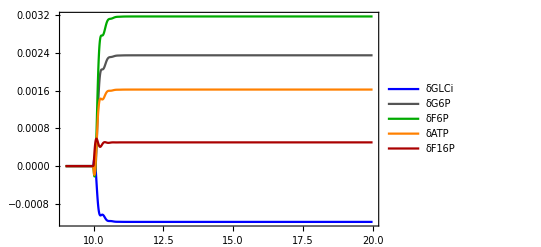

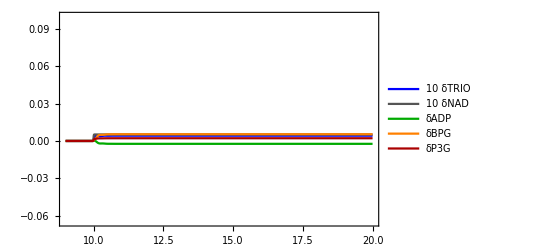

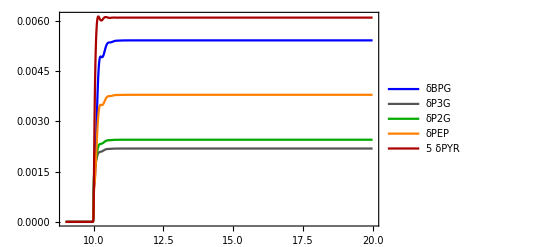

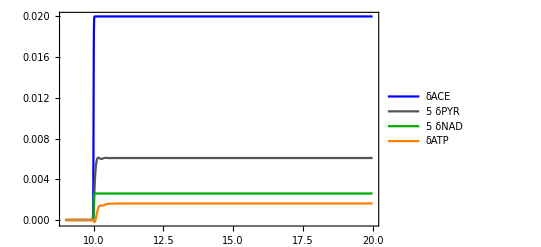

```mathematica
(*Step perturbation of ACE level, and the response of mitobolite concentration*)
	
w0=21;
t0=10;
maxTime=20;
hill=2000;
glco0=2;
aceAmp0=0.16;
ace[t_]:=aceAmp0*(1+0.02*t^hill/(t0^hill+t^hill));
(*ace[t_]:=0.05*(1+0.02*Sin[w0 t]);*)
output=glycolysisACE[ace,maxTime,glco0];
Time0=Array[0.01  #1 +t0-2&,100];
ace1=Mean[Table[ace[t],{t,Time0}]];
amp1=Mean[Table[amp[t],{t,Time0}]];
atp1=Mean[Table[atp[t],{t,Time0}]];
bpg1=Mean[Table[bpg[t],{t,Time0}]];
f16p1=Mean[Table[f16p[t],{t,Time0}]];
f6p1=Mean[Table[f6p[t],{t,Time0}]];
g3p1=Mean[Table[g3p[t],{t,Time0}]];
g6p1=Mean[Table[g6p[t],{t,Time0}]];
glci1=Mean[Table[glci[t],{t,Time0}]];
nadh1=Mean[Table[nadh[t],{t,Time0}]];
p2g1=Mean[Table[p2g[t],{t,Time0}]];
p3g1=Mean[Table[p3g[t],{t,Time0}]];
pep1=Mean[Table[pep[t],{t,Time0}]];
pyr1=Mean[Table[pyr[t],{t,Time0}]];
trio1=Mean[Table[trio[t],{t,Time0}]];
adp1=Mean[Table[adp[t],{t,Time0}]];
nad1=Mean[Table[nad[t],{t,Time0}]];


results=Table[rates//.rateEquations//.assignments//.parameters//.timeCourse,{t,{20}}];
results2=Flatten[Flatten[results]];
MatrixForm[Reverse[SortBy[Transpose[{{"GLT","GLK","GLYCO","Treha",
"PGI", "PFK","ALD","G3PDH", "G3PP",
"GAPDH", "PGK", "PGM",  "ENO","PYK",
"PDC", "SUC", "ADH",   "ATPase","AK"},results2}],Last]]]

results=Table[variables//.assignments//.parameters//.timeCourse,{t,{20}}];
results2=Flatten[Flatten[results]];
MatrixForm[Reverse[SortBy[Transpose[{{ "AMP", "ATP", "BPG", "F16P", "F6P"," G3P", "G6P", "GLCi","NADH", "P2G", "P3G", "PEP", "PYR", "TRIO"},results2}],Last]]]

(*Plot[{(ace[t]-ace1),  (nadh[t]-nadh1),(atp[t]-atp1)},{t,t0-2,maxTime},PlotRange->Full,PlotLegends->{"ΔACE","ΔNADH","ΔATP"}]

Plot[{(ace[t]-ace1),(amp[t]-amp1),  (atp[t]-atp1),(bpg[t]-bpg1),0.1(f16p[t]-f16p1),(f6p[t]-f6p1),(g3p[t]-g3p1),(g6p[t]-g6p1),(glci[t]-glci1),(nadh[t]-nadh1),(p2g[t]-p2g1),(p3g[t]-p3g1),(pep[t]-pep1),(pyr[t]-pyr1),(trio[t]-trio1)},{t,t0-2,maxTime},PlotRange->Full,PlotLegends->{"ACE","AMP","ATP","BPG","F16P","F6P","G3P","G6P","GLCi","NADH","P2G","P3G","PEP","PYR","TRIO"}]*)

(*{Black,Thickness[0.01]},{Blue,Thickness[0.01]},{Orange,Thickness[0.01]},{Red,Thickness[0.01]},{Purple,Thickness[0.01]},{Darker[Green],Thickness[0.01]}*)
Plot[{(glci[t]-glci1)/glci1,  (g6p[t]-g6p1)/g6p1,(f6p[t]-f6p1)/f6p1,(atp[t]-atp1)/atp1,(f16p[t]-f16p1)/f16p1},{t,t0-1,maxTime},PlotRange->Full,PlotLegends->{"δGLCi","δG6P","δF6P","δATP","δF16P"},PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]

Plot[{10(trio[t]-trio1)/trio1,10(nad[t]-nad1)/nad1,(adp[t]-adp1)/adp1,(bpg[t]-bpg1)/bpg1,(p3g[t]-p3g1)/p3g1},{t,t0-1,maxTime},PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},PlotRange->{-0.065,0.1},PlotLegends->{"10 δTRIO","10 δNAD","δADP","δBPG","δP3G"},BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
(*Plot[{(trio[t]-trio1)/trio1,  (nad[t]-nad1)/nad1,(bpg[t]-bpg1)/bpg1,(adp[t]-adp1)/adp1,(p3g[t]-p3g1)/p3g1},{t,t0,t0+4 Pi/w0},PlotRange->Full,PlotLegends->{"TRIO","NAD","BPG","ADP","ATP","P3G"}]*)

Plot[{(bpg[t]-bpg1)/bpg1,  (p3g[t]-p3g1)/p3g1,(p2g[t]-p2g1)/p2g1,(pep[t]-pep1)/pep1,5(pyr[t]-pyr1)/pyr1},{t,t0-1,maxTime},PlotRange->Full,PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},PlotLegends->{"δBPG","δP3G","δP2G","δPEP","5 δPYR"},BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]

Plot[{(ace[t]-ace1)/ace1,  5(pyr[t]-pyr1)/pyr1,5(nad[t]-nad1)/nad1,(atp[t]-atp1)/atp1},{t,t0-1,maxTime},PlotRange->Full,PlotLegends->{"δACE","5 δPYR","5 δNAD","δATP"},PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
```

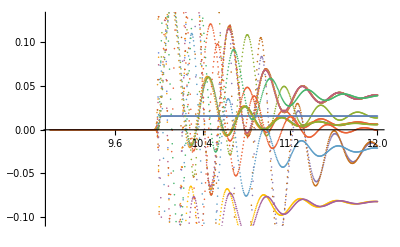

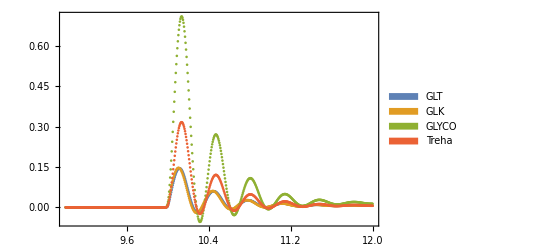

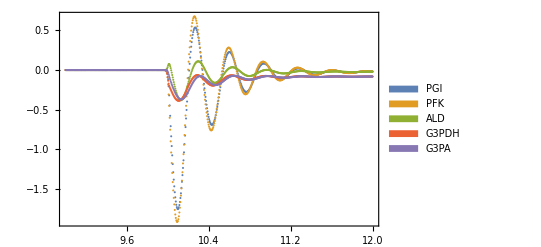

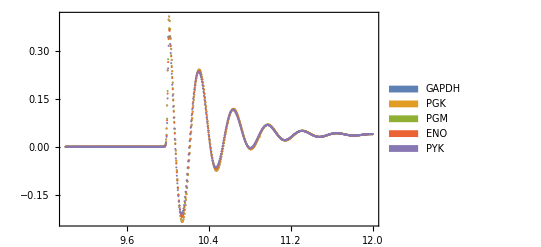

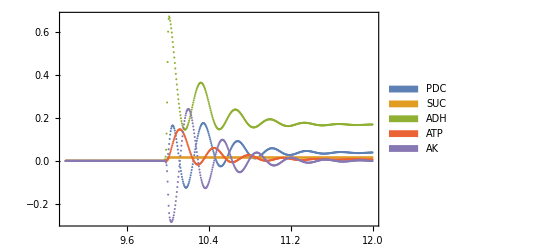

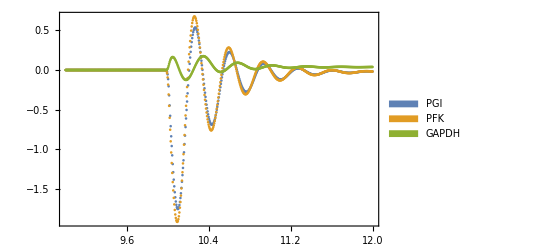

```mathematica
(** the response of flux to from the step perturbation specified above **)

xx=Table[0.005 x+t0-1,{x,600}];
result=Array[0 #1 &,19];
meanResult=Array[0 #1 &, 19];
For[j=1,j<20,j++,result[[j]]=Flatten[Table[rates[[j]]//.rateEquations//.assignments//.parameters//.timeCourse,{t,xx}]]];
For[j=1,j<20,j++,
meanResult[[j]]=Mean[result[[j,1;;100]]]];
ListPlot[Table[Thread[{xx,result[[j]]-meanResult[[j]]}],{j,19}]]


ListPlot[Table[Thread[{xx,result[[j]]-meanResult[[j]]}],{j,4}],PlotRange->Full,PlotLegends->Placed[SwatchLegend[{"GLT","GLK","GLYCO","Treha"},LegendMarkerSize->7,LegendMarkers->"Bubble"],Right],BaseStyle->{FontSize->15},Frame->True]
ListPlot[Table[Thread[{xx,result[[j]]-meanResult[[j]]}],{j,{5,6,7,8,9}}],PlotRange->Full,PlotLegends->SwatchLegend[{"PGI","PFK","ALD","G3PDH","G3PA"},LegendMarkerSize->7,LegendMarkers->"Bubble"],BaseStyle->{FontSize->15},Frame->True]
ListPlot[Table[Thread[{xx,result[[j]]-meanResult[[j]]}],{j,{10,11,12,13,14}}],PlotRange->Full,PlotLegends->SwatchLegend[{"GAPDH","PGK","PGM","ENO","PYK"},LegendMarkerSize->7,LegendMarkers->"Bubble"] ,BaseStyle->{FontSize->15},Frame->True]
ListPlot[Table[Thread[{xx,result[[j]]-meanResult[[j]]}],{j,{15,16,17,18,19}}],PlotRange->Full,PlotLegends->SwatchLegend[{"PDC","SUC","ADH","ATP","AK"},LegendMarkerSize->7,LegendMarkers->"Bubble"],BaseStyle->{FontSize->15},Frame->True]
ListPlot[Table[Thread[{xx,result[[j]]-meanResult[[j]]}],{j,{5,6,15}}],PlotRange->Full,PlotLegends->SwatchLegend[{"PGI","PFK","GAPDH"},LegendMarkerSize->7,LegendMarkers->"Bubble"],BaseStyle->{FontSize->15},Frame->True]
```

```mathematica
(*Analyze the phase diagram to step perturbation: adaptation error etc. It is very slow...*)
(*To plot the phase diagram for the model without GLYO, i.e., SUCC, flux, use the model glycolysisACEremoveGLYCO *)
ComputePhaseDiagram:=(
t0=8;
maxTime=t0+5;
hill=200;
s1=40;s2=47;
glcoArray=Array[0.2 #1 +2.3&,s1];
aceAmpArray=Array[0.02#1+0.023 &,s2];
(*s1=20;s2=38;
glcoArray=Array[0.2 #1 +1.8&,s1];
aceAmpArray=Array[0.02#1+0.04 &,s2];*)
resultAdaptation=Table[0 x+0 y,{x,s2 s1},{y,6}];
s=1;
For[j=1,j<s1+1,j++,
For[k=1,k<s2+1,k++,
glco0=glcoArray[[j]];
aceAmp0=aceAmpArray[[k]];
ace[t_]:=aceAmp0*(1+0.02*t^hill/(t0^hill+t^hill));
out=glycolysisACE[ace,maxTime,glco0];
outPYR=AnalyzeAdaptation[pyr,t0,2];
outATP=AnalyzeAdaptation[atp,t0,2];
resultAdaptation[[s,1]]=glco0;
resultAdaptation[[s,2]]=aceAmp0;
resultAdaptation[[s,3]]=outATP[[1]];(* adaptation error of ATP *)
resultAdaptation[[s,4]]=outATP[[2]];(* oscillation index of ATP *)
resultAdaptation[[s,5]]=outPYR[[1]];(* adaptation error of PYR *)
resultAdaptation[[s,6]]=outPYR[[2]];(* oscillation index of PYR *)
s++;]]

(*Plot the phase diagram to step perturbation*)
ListContourPlot[resultAdaptation[[All,1;;3]],PlotLabel->"adaptation error of ATP",AxesLabel->{"Cluco","ACE0"},Contours->10,PlotLegends->Automatic,BaseStyle->{FontSize->15}]
ListContourPlot[resultAdaptation[[All,{1,2,4}]],PlotLabel->"oscillation index of ATP",AxesLabel->{"Cluco","ACE0"},Contours->5,PlotLegends->Automatic,BaseStyle->{FontSize->15}]
ListContourPlot[resultAdaptation[[All,{1,2,5}]],PlotLabel->"adaptation error of PYR",AxesLabel->{"Cluco","ACE0"},Contours->3,PlotLegends->Automatic,BaseStyle->{FontSize->15}]
ListContourPlot[resultAdaptation[[All,{1,2,6}]],PlotLabel->"oscillation index of PYR",AxesLabel->{"Cluco","ACE0"},Contours->5,PlotLegends->Automatic,BaseStyle->{FontSize->15}]

(*Compute the phase diagraph of phase shift under periodic perturbation*)

w0=20;
t0=5;
maxTime=t0+10 Pi/w0;
hill=200;
s1=40;s2=47;
glcoArray=Array[0.2 #1 +2.3&,s1];
aceAmpArray=Array[0.02#1+0.023 &,s2];
resultPYRphase=Table[0 x+0 y,{x,s2 s1},{y,4}];
s=1;
For[j=1,j<s1+1,j++,
For[k=1,k<s2+1,k++,
glco0=glcoArray[[j]];
aceAmp0=aceAmpArray[[k]];
(*ace[t_]:=0.18*(1+0.1*t^hill/(t0^hill+t^hill));*)
ace[t_]:=aceAmp0*(1+0.02*Sin[w0 t]);
output=glycolysisACE[ace,maxTime,glco0];
out2=detectPhaseShift2[ace,pyr,t0,w0];
resultPYRphase[[s,1]]=glco0;
resultPYRphase[[s,2]]=aceAmp0;
resultPYRphase[[s,3]]=out2[[7]];
resultPYRphase[[s,4]]=out2[[4]];
s++;]];
{resultAdaptation,resultPYRphase})
```

```mathematica
(*Export and importing data for plotting the phase diagram*)
SetDirectory[NotebookDirectory[]]
AppendTo[$Path,FileNameJoin[{Directory[]}]];

file="glycoACEpert_Phase_diagram.dat";
(*check file existendce, if exist, import; otherwise, compute it*)
If [FileExistsQ[file],Get[file],{resultAdaptation,resultPYRphase}=ComputePhaseDiagram;
 Save[StringJoin[Directory[],"/",file],{resultAdaptation,resultPYRphase}]]
```

/Users/shouwenwang/Dropbox (HMS)/Projects in PhD/collective oscillations/code_for_collective_oscillations/my_code_for_glycolysis/Final model for glycolysis

{{2.5,0.043,-0.36374,0.0163592},{2.5,0.063,-0.135436,0.0133389},{2.5,0.083,0.046621,0.0111158},1875,{10.3,0.943,-2.89177,0.032272},{10.3,0.963,-2.86406,0.0306797}}
 |  |  |  |

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961]}

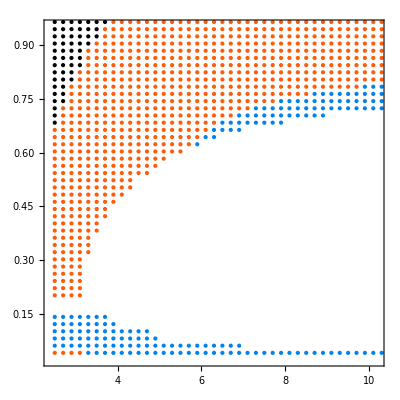

```mathematica
(******** Plot the phase diagram combining both adaptation error and phase shift ********)

PhaseDiagram=Table[0 x+0 y,{x,Length[resultPYRphase]},{y,3}];
errorR=0.5;osciR=0.1;
color=ColorData[3,"ColorList"][[{1,2,4,6,8}]]
For[j=1,j<Length[resultAdaptation]+1,j++,PhaseDiagram[[j,1]]=resultAdaptation[[j,1]];
PhaseDiagram[[j,2]]=resultAdaptation[[j,2]];temp=color[[1]];(*nothing*)
If[resultAdaptation[[j,3]]<errorR && resultAdaptation[[j,4]]<osciR ,temp=color[[2]]]; (*only adaptation *)
If[resultPYRphase[[j,3]]>0 && resultAdaptation[[j,4]]<osciR ,temp=color[[4]]]; (*only phase lead*)
If[resultPYRphase[[j,3]]>0 && resultAdaptation[[j,3]]<errorR && resultAdaptation[[j,4]]<osciR ,temp=color[[4]]]; (* hase lead + adaptation *)
(****************** change the lower back regime to blue *****************)
If[PhaseDiagram[[j,2]]>=0.05 && PhaseDiagram[[j,2]]<0.16,temp=color[[4]]]; 
(****************** change the lower back around ACE=0.2 regime to white*****************)
If[PhaseDiagram[[j,2]]>=0.16 && PhaseDiagram[[j,2]]<0.19,temp=White]; 
(****************** change the lower back regime to blue *****************)
If[resultAdaptation[[j,4]]>osciR,temp=White]; (* oscillation *)
PhaseDiagram[[j,3]]=temp];

h=PhaseDiagram[[All,{1,2}]];
c=Flatten[PhaseDiagram[[All,{3}]]];
colorfunc=ColorData["TemperatureMap"];
Graphics[{PointSize[Large],#[[1]],Point[#[[2]]]}&/@Transpose[{c,h}],PlotRange->{{2.4,10.2},{0.025,0.95}},AspectRatio->1,Frame->True,BaseStyle->{FontSize->20}]
```

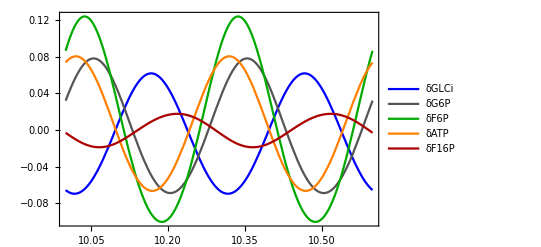

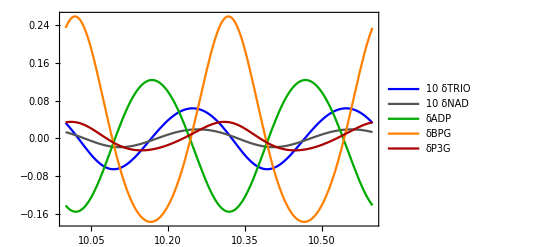

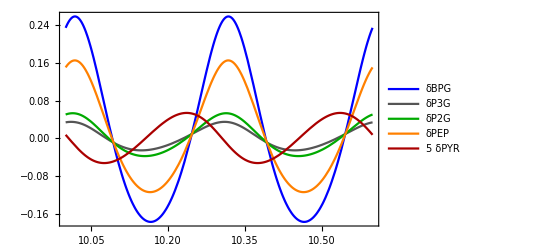

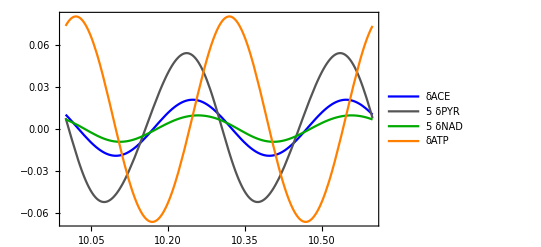

```mathematica
(*Compute the resposen to periodic perturbation*)

t0=10;
w0=21;
maxTime=t0+4 Pi/w0;
glco0=10;(*glcoArray[[j]];*)
aceAmp0=0.05;(*aceAmpArray[[k]];*)
(*ace[t_]:=0.18*(1+0.1*t^hill/(t0^hill+t^hill));*)
ace[t_]:=aceAmp0*(1+0.02*Sin[w0 t]);
output=glycolysisACE[ace,maxTime,glco0];
out2=detectPhaseShift2[ace,pyr,t0,w0];
Time0=Array[0.01  #1 +t0-2&,100];
ace1=Mean[Table[ace[t],{t,Time0}]];
amp1=Mean[Table[amp[t],{t,Time0}]];
atp1=Mean[Table[atp[t],{t,Time0}]];
bpg1=Mean[Table[bpg[t],{t,Time0}]];
f16p1=Mean[Table[f16p[t],{t,Time0}]];
f6p1=Mean[Table[f6p[t],{t,Time0}]];
g3p1=Mean[Table[g3p[t],{t,Time0}]];
g6p1=Mean[Table[g6p[t],{t,Time0}]];
glci1=Mean[Table[glci[t],{t,Time0}]];
nadh1=Mean[Table[nadh[t],{t,Time0}]];
p2g1=Mean[Table[p2g[t],{t,Time0}]];
p3g1=Mean[Table[p3g[t],{t,Time0}]];
pep1=Mean[Table[pep[t],{t,Time0}]];
pyr1=Mean[Table[pyr[t],{t,Time0}]];
trio1=Mean[Table[trio[t],{t,Time0}]];
adp1=Mean[Table[adp[t],{t,Time0}]];
nad1=Mean[Table[nad[t],{t,Time0}]];

Plot[{(glci[t]-glci1)/glci1,  (g6p[t]-g6p1)/g6p1,(f6p[t]-f6p1)/f6p1,(atp[t]-atp1)/atp1,(f16p[t]-f16p1)/f16p1},{t,t0,maxTime},PlotRange->Full,PlotLegends->{"δGLCi","δG6P","δF6P","δATP","δF16P"},PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]

Plot[{10(trio[t]-trio1)/trio1,10(nad[t]-nad1)/nad1,(adp[t]-adp1)/adp1,(bpg[t]-bpg1)/bpg1,(p3g[t]-p3g1)/p3g1},{t,t0,maxTime},PlotRange->Full,PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},PlotLegends->{"10 δTRIO","10 δNAD","δADP","δBPG","δP3G"},BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
(*Plot[{(trio[t]-trio1)/trio1,  (nad[t]-nad1)/nad1,(bpg[t]-bpg1)/bpg1,(adp[t]-adp1)/adp1,(p3g[t]-p3g1)/p3g1},{t,t0,t0+4 Pi/w0},PlotRange->Full,PlotLegends->{"TRIO","NAD","BPG","ADP","ATP","P3G"}]*)

Plot[{(bpg[t]-bpg1)/bpg1,  (p3g[t]-p3g1)/p3g1,(p2g[t]-p2g1)/p2g1,(pep[t]-pep1)/pep1,5(pyr[t]-pyr1)/pyr1},{t,t0,maxTime},PlotRange->Full,PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},PlotLegends->{"δBPG","δP3G","δP2G","δPEP","5 δPYR"},BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]

Plot[{(ace[t]-ace1)/ace1,  5(pyr[t]-pyr1)/pyr1,5(nad[t]-nad1)/nad1,(atp[t]-atp1)/atp1},{t,t0,maxTime},PlotRange->Full,PlotLegends->{"δACE","5 δPYR","5 δNAD","δATP"},PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
```

```mathematica
(*Compute the phase shift at different frequencies*)

(*w0=Array[0.1 1.5^#1 &,runN]*)
t0=5;
w1={0.2,0.3,0.4,0.6,0.8,1.2,1.6,2.5,3.2,4.5,6.4,8,10,13,15,17,18,20,22,23,25,27,29,32,35,37,42,48,55,63,82,106,138,179,233,303,394,512,665,865,1125,1462,1900,3000,4000,5000,6000,8000,10000,15000,20000,30000,50000,100000};
(*w0=w1[[1;;runN]];*)
w0={0.2,0.7,1.2,1.7,2.2,2.7,3.2,3.7,4.2,4.7,5.2,5.7,6.2,6.7,7.2,7.7,8.2,8.7,9.2,9.7,10.2,10.7,11.2,11.7,12.2,12.7,13.2,13.7,14.2,14.7,15.2,15.7,16.2,16.7,17.2,17.7,18.2,18.7,19.2,19.7,20.2,20.7,21.2,21.7,22.2,22.7,23.2,23.7,24.2,24.7,25.2,25.7,26.2,26.7,27.2,27.7,28.2,28.7,29.2,29.7,30.2,30.7,31.2,31.7,32.2,32.7,33.2,33.7,34.2,34.7,35.2,35.7,36.2,36.7,37.2,37.7,38.2,38.7,39.2,39.7};
NSpecies=16;
runN=Length[w0];
result=Table[0 x+0y+0z,{x,runN},{y,NSpecies},{z,3}];
output=Table[0 x,{x,NSpecies}];
For[i=1,i<=runN, i++,
maxTime=t0+10 Pi/w0[[i]];
hill=50;
ace[t_]:=aceAmp0*(1+0.02*Sin[w0[[i]] t]);
out1=glycolysisACE[ace,maxTime,glco0];
(*Plot[{(nadh[t]-nadh1),  (atp[t]-atp1),(ace[t]-ace1)},{t,5,5+10/w0},PlotLegends->{"NADH","ATP","ACE"}]*)
output[[1]]=detectPhaseShift2[ace,amp,t0,w0[[i]]];
output[[2]]=detectPhaseShift2[ace,atp,t0,w0[[i]]];
output[[3]]=detectPhaseShift2[ace,bpg,t0,w0[[i]]];
output[[4]]=detectPhaseShift2[ace,f16p,t0,w0[[i]]];
output[[5]]=detectPhaseShift2[ace,f6p,t0,w0[[i]]];
output[[6]]=detectPhaseShift2[ace,g3p,t0,w0[[i]]];
output[[7]]=detectPhaseShift2[ace,g6p,t0,w0[[i]]];
output[[8]]=detectPhaseShift2[ace,glci,t0,w0[[i]]];
output[[9]]=detectPhaseShift2[ace,nadh,t0,w0[[i]]];
output[[10]]=detectPhaseShift2[ace,p2g,t0,w0[[i]]];
output[[11]]=detectPhaseShift2[ace,p3g,t0,w0[[i]]];
output[[12]]=detectPhaseShift2[ace,pep,t0,w0[[i]]];
output[[13]]=detectPhaseShift2[ace,pyr,t0,w0[[i]]];
output[[14]]=detectPhaseShift2[ace,trio,t0,w0[[i]]];
output[[15]]=detectPhaseShift2[ace,adp,t0,w0[[i]]];
output[[16]]=detectPhaseShift2[ace,nad,t0,w0[[i]]];
For[j=1,j<NSpecies+1,j++,
result[[i,j,1]]=output[[j,2]]; 
result[[i,j,2]]=output[[j,4]]/output[[j,3]];   (*response amplitude*)
result[[i,j,3]]=output[[j,7]]]]; (*phase shift*)
```

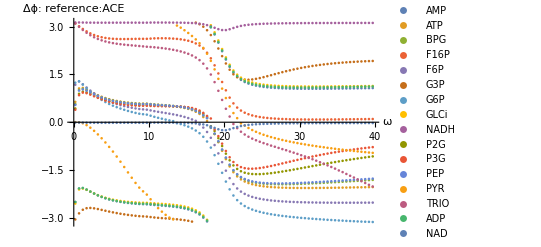

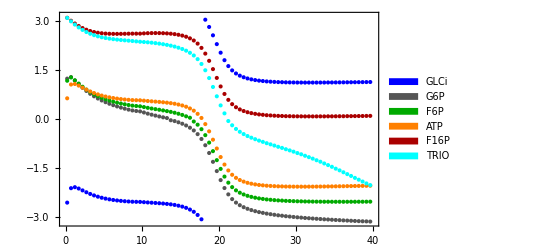

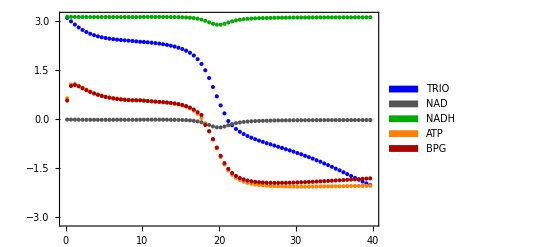

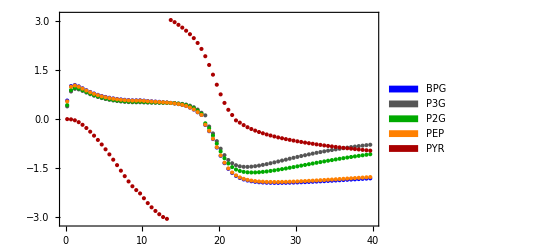

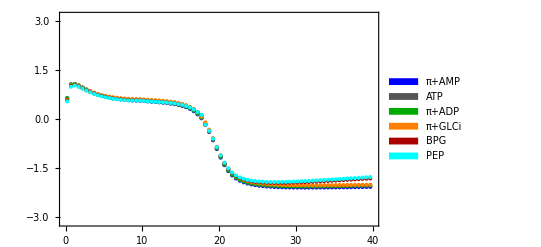

```mathematica
(*%%%%%%%%%%%%%%%%%%%% PLOT FIGURES for phase shift %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
ty=3;(*phase shift*)
bg=1;ed=Length[w0];
ListPlot[{Thread[{w0[[bg;;ed]],result[[bg;;ed,1,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,2,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,3,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,4,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,5,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,6,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,7,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,8,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,9,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,10,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,11,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,12,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,13,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,14,ty]]}],
Thread[{w0[[bg;;ed]],result[[bg;;ed,15,ty]]}],Thread[{w0[[bg;;ed]],result[[bg;;ed,16,ty]]}]},PlotRange->All,AxesLabel->{"ω","Δϕ: reference:ACE"},PlotLegends->{"AMP","ATP","BPG","F16P","F6P","G3P","G6P","GLCi","NADH","P2G","P3G","PEP","PYR","TRIO","ADP","NAD"},PlotStyle->{Thick}]



ListPlot[{Thread[{w0,result[[All,8,ty]]}],Thread[{w0,result[[All,7,ty]]}],Thread[{w0,result[[All,5,ty]]}],Thread[{w0,result[[All,2,ty]]}],Thread[{w0,result[[All,4,ty]]}],Thread[{w0,result[[All,14,ty]]}]},PlotRange->{{0,40},{-Pi,Pi}},PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red],Cyan,Brown,Red},PlotLegends->SwatchLegend[{"GLCi","G6P","F6P","ATP","F16P","TRIO"},LegendMarkerSize->7,LegendMarkers->"Bubble"],BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]


ListPlot[{Thread[{w0,result[[All,14,ty]]}],Thread[{w0,result[[All,16,ty]]}],Thread[{w0,result[[All,9,ty]]}],Thread[{w0,result[[All,2,ty]]}],Thread[{w0,result[[All,3,ty]]}]},PlotRange->{{0,40},{-Pi,Pi}},PlotLegends->SwatchLegend[{"TRIO","NAD","NADH","ATP","BPG"},LegendMarkerSize->7,LegendMarkers->"Bubble"],PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]

ListPlot[{Thread[{w0,result[[All,3,ty]]}],Thread[{w0,result[[All,11,ty]]}],Thread[{w0,result[[All,10,ty]]}],Thread[{w0,result[[All,12,ty]]}],Thread[{w0,result[[All,13,ty]]}]},PlotRange->{{0,40},{-Pi,Pi}},PlotLegends->SwatchLegend[{"BPG","P3G","P2G","PEP","PYR"},LegendMarkerSize->7,LegendMarkers->"Bubble"],PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]

ListPlot[{Thread[{w0,Mod[result[[All,1,ty]],2 Pi]-Pi}],Thread[{w0,Mod[result[[All,2,ty]]+Pi,2Pi]-Pi}],Thread[{w0,Mod[result[[All,15,ty]],2 Pi]-Pi}],Thread[{w0,Mod[result[[All,8,ty]],2 Pi]-Pi}],Thread[{w0,Mod[result[[All,3,ty]]+Pi,2 Pi]-Pi}],Thread[{w0,Mod[result[[All,12,ty]]+Pi,2 Pi]-Pi}]},PlotRange->{{0,40},{-Pi,Pi}},PlotLegends->SwatchLegend[{"π+AMP","ATP","π+ADP","π+GLCi","BPG","PEP"},LegendMarkerSize->7,LegendMarkers->"Bubble"],PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red],Cyan},BaseStyle->{FontSize->15},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]

(*ListPlot[{Thread[{w0,result[[All,16,ty]]}],Thread[{w0,result[[All,3,ty]]}],Thread[{w0,result[[All,2,ty]]}],Thread[{w0,result[[All,13,ty]]}]},PlotRange->All,PlotLegends->{"NAD","BPG","ATP","PYR"},BaseStyle->{FontSize->15},Frame->True]*)
```

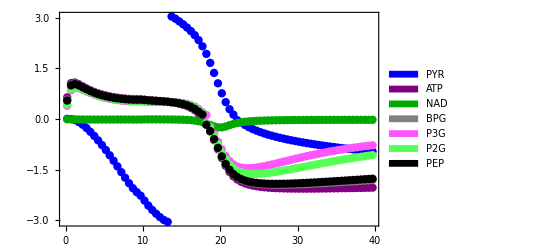

```mathematica
(*%%%%%%%%%%%%%%%% Plot the phase shift used in the main text %%%%%%%%%%%%%%%%%%%%%%%%%*)

ListPlot[{Thread[{w0,result[[All,13,ty]]}],Thread[{w0,result[[All,2,ty]]}],Thread[{w0,result[[All,16,ty]]}],Thread[{w0,result[[All,3,ty]]}],Thread[{w0,result[[All,11,ty]]}],Thread[{w0,result[[All,10,ty]]}],Thread[{w0,result[[All,12,ty]]}]},PlotRange->All,PlotLegends->SwatchLegend[{"PYR","ATP","NAD","BPG","P3G","P2G","PEP"},LegendMarkerSize->8,LegendMarkers->"Bubble"],BaseStyle->{FontSize->15},PlotStyle->{{Blue,PointSize[0.015]},{Purple,PointSize[0.015]},{Darker[Green],PointSize[0.015]},{Gray,PointSize[0.015]},{Lighter[Magenta],PointSize[0.015]},{Lighter[Green],PointSize[0.015]},{Black,PointSize[0.015]}},Frame->True,Axes->True]
```

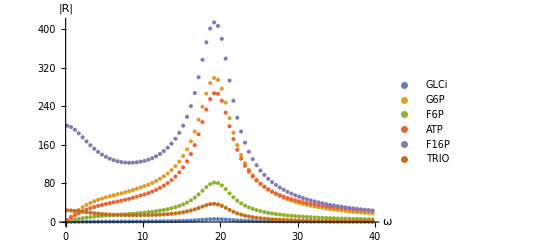

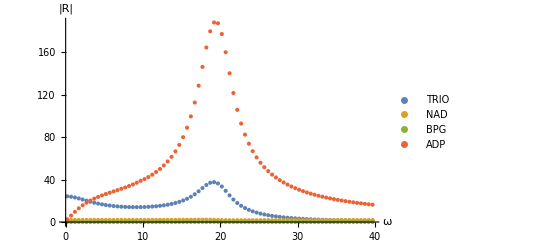

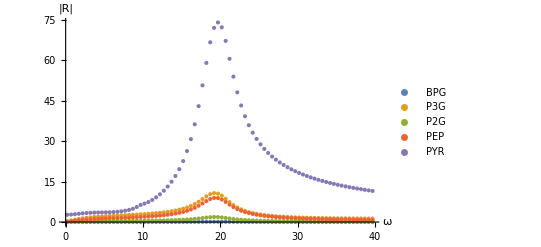

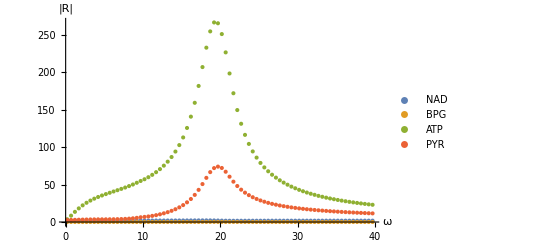

```mathematica
(*%%%%%%%%%%%%%%%% Plot the response amplitude %%%%%%%%%%%%%%%%%%%%%%%%%*)
ty=2;  (*response amplitude*)
ListPlot[{Thread[{w0,result[[All,8,ty]]}],Thread[{w0,result[[All,7,ty]]}],Thread[{w0,result[[All,5,ty]]}],Thread[{w0,result[[All,2,ty]]}],Thread[{w0,result[[All,4,ty]]}],Thread[{w0,result[[All,14,ty]]}]},PlotRange->All,AxesLabel->{"ω","|R|"},PlotLegends->{"GLCi","G6P","F6P","ATP","F16P","TRIO"}]
ListPlot[{Thread[{w0,result[[All,14,ty]]}],Thread[{w0,result[[All,16,ty]]}],Thread[{w0,result[[All,3,ty]]}],Thread[{w0,result[[All,15,ty]]}]},PlotRange->All,AxesLabel->{"ω","|R|"},PlotLegends->{"TRIO","NAD","BPG","ADP"}]
ListPlot[{Thread[{w0,result[[All,3,ty]]}],Thread[{w0,result[[All,11,ty]]}],Thread[{w0,result[[All,10,ty]]}],Thread[{w0,result[[All,12,ty]]}],Thread[{w0,result[[All,13,ty]]}]},PlotRange->All,AxesLabel->{"ω","|R|"},PlotLegends->{"BPG","P3G","P2G","PEP","PYR"}]
ListPlot[{Thread[{w0,result[[All,16,ty]]}],Thread[{w0,result[[All,3,ty]]}],Thread[{w0,result[[All,2,ty]]}],Thread[{w0,result[[All,13,ty]]}]},PlotRange->All,AxesLabel->{"ω","|R|"},PlotLegends->{"NAD","BPG","ATP","PYR"}]
```